# NIUS project calculations

## Done by: Soumyadeep Sarma, Project under: Prof. Deepak Dhar

```mathematica
L=3;
f[z_]= Sum[Binomial[L-n+1,n] z^n,{n,0,(L+1)/2}]
s =Roots[f[z]==0,z]//FullSimplify;
t =NRoots[f[z]==0,z]//FullSimplify;
```

1+3 z+z^2

```mathematica
Solve[f[z]==0,z]//FullSimplify;
```

```mathematica
Solve[N[s[[2]],10]](*Checking for the roots*)
```

{{z→-0.26794919}}

```mathematica
g[z_]= Sum[Binomial[L-n+1,n] z^n,{n,1,(L+1)/2}];
k = Roots[g[z]==0,z]//FullSimplify;
Solve[N[k[[2]],10]]
```

{{z→-0.480508462-0.400470217 ⅈ}}

Diagonalizing T matrix for dimer on ladder problem

```mathematica
Clear[z]
```

```mathematica
l=100;
```

```mathematica
T=({{1+y, 1, 1}, {2y, y, 0}, {y^2, 0, 0}});
t=Eigenvalues[T];
w =Eigenvectors[T];
Subscript[v, i] = {1+y,2y,y^2};
v = MatrixPower[T,l-1].Subscript[v, i];
f[y_]=y;
g[y_]=v[[1]]//Expand
j = Roots[g[y]==0,y]//FullSimplify;
```

1+298 y+43661 y^2+4192634 y^3+296799341 y^4+16518209710 y^5+752708358868 y^6+28880039162730 y^7+952221952533068 y^8+27402662047997278 y^9+696722613277535951 y^10+15805412606984564386 y^11+322503167803010347894 y^12+5958925769948891158080 y^13+100272120602041287842938 y^14+1544133373461553209611432 y^15+21852777746932207330958831 y^16+285255103404132639529272106 y^17+3445528963114173584889849762 y^18+38618856931697557311671103714 y^19+402669573968506745855069368733 y^20+3914430615268475023645690020176 y^21+35548331566896099501085249352880 y^22+302113755900755857873748243166176 y^23+2406648740718611008605057189079186 y^24+17995579708069249566684475417834852 y^25+126469966094768102828366537726318309 y^26+836332519180608710739644138731097532 y^27+5209450045053702557783211358695995196 y^28+30593690295840312534223243899656290830 y^29+169536549222246275834698201963845776238 y^30+887182262315062023940859522265042431042 y^31+4387046003742698362977890942887455369473 y^32+20511671359265870745633697093884174929700 y^33+90725497235169527814103692386369961504656 y^34+379803783824514749519916282860282652319368 y^35+1505452416862848335663377601674493698908519 y^36+5652028552793202205345740214299387220928842 y^37+20104805774767869279564484553606453626428756 y^38+67773569767171557026851097948099671904946750 y^39+216556685408777376411636490553936404770404960 y^40+655993230777384448925067555295642365392105570 y^41+1884040087006736884066695015043431719574164910 y^42+5130642903986189946084772650131866039573226630 y^43+13248113901056422647923954387911051205811392100 y^44+32436129327101407872919056603945112487874309510 y^45+75295927774862053274406583679258973768140972680 y^46+165706374991623792446413492291688753387995389250 y^47+345679120849464183750215383423985464903980508630 y^48+683435489977155846277523770322639023727384936130 y^49+1280324187269695813632616765874392482232104392308 y^50+2272120470228779257012291402081611029349460711838 y^51+3818615547318219674094912378123670017828473076386 y^52+6075765460954357837693394122642319213404010490574 y^53+9148644315762694992345371742608907613285939438956 y^54+13031546737202451218841774393426068594587637900010 y^55+17551883212119188519408552409562464289957325201508 y^56+22342248610605497627758048698152172267332949352350 y^57+26864182844455768668283821219653375933393309431378 y^58+30493895467143442771976175095978944991204406703978 y^59+32656804287785477554142682751636373944253207104296 y^60+32973439596030289131961397725731562932497368966066 y^61+31366881797027804188584423209260712594848736555664 y^62+28090481214885141524791317588540423692903536331430 y^63+23662921023014338424192379938059704375223109541953 y^64+18733316097414927622867778028020648328617999865132 y^65+13924759856750725467688085574965935981061400363771 y^66+9708439623398173303430552862999682792025690425776 y^67+6342089251628815464836175282506177695707420184497 y^68+3877373967321006867951312483363815408280747768564 y^69+2215813709052131804585328001608674579870760734688 y^70+1182091105887529250425739670370408798165733365596 y^71+587873873050566125507223517005280186202581867660 y^72+272135095737535099439963974553938828976703115276 y^73+117073503182760889896833065676600987690948840096 y^74+46726535481366217238203232301075296603278237748 y^75+17270416545353278682986068767918967668910428676 y^76+5899570390811652056293514462102725442082342548 y^77+1858638066975428902114908962608259807017811944 y^78+538805113491334297656441343159893803749161820 y^79+143368883954867940797464861727650612971211562 y^80+34921759989188404468134894732126572663340968 y^81+7763941842259754348038679403645797438836862 y^82+1570435329360208092344597448491546572185520 y^83+287989703155242024299935341609589355868634 y^84+47693316426202676350652427243788930831352 y^85+7101879523322452310579537311753191609256 y^86+946246518404718184518856136589025218728 y^87+112188567744414319069574070506879985764 y^88+11761304612138164736600074228062584560 y^89+1082267427222641841333314290276568420 y^90+86662169032989195993907596769641920 y^91+5976371804934218581452313263900260 y^92+350463223892109214279481147535680 y^93+17198976780821041383686223984600 y^94+691803586558623431163252505280 y^95+22171343624194471693899854905 y^96+543463907147521622407750090 y^97+9551836817697981604340045 y^98+107007320510432596513850 y^99+573147844013817084101 y^100

```mathematica
data = Table[f[y]/.Solve[N[j[[i]],10]],{i,1,l}]
```

{{-15.99580581},{-15.29744975},{-14.25743769},{-13.01468493},{-11.69890321},{-10.40822254},{-9.204216048},{-8.117660108},{-7.15783679},{-6.321087594},{-5.597095894},{-4.972907805},{-4.435240229},{-3.971661351},{-3.571095224},{-3.22395189},{-2.92206751},{-2.658560431},{-2.427660563},{-2.224541025},{-2.045165166},{-1.886153571},{-1.744671357},{-1.618334159},{-1.505130391},{-1.403357322},{-1.311568629},{-1.228531407},{-1.153190898},{-1.084641527},{-1.022103053},{-0.9649008905},{-0.9124498251},{-0.8642404966},{-0.8198281453},{-0.7788232116},{-0.7408834613},{-0.7057073653},{-0.673028519},{-0.6426109234},{-0.6142449832},{-0.5877441033},{-0.562941788},{-0.5396891611},{-0.517852842},{-0.4973131226},{-0.4779623986},{-0.4597038186},{-0.4424501162},{-0.4261226008},{-0.410650281},{-0.3959691024},{-0.3820212819},{-0.3687547223},{-0.3561224957},{-0.3440823823},{-0.3325964556},{-0.3216307032},{-0.3111546783},{-0.3011411727},{-0.2915659087},{-0.282407245},{-0.273645895},{-0.2652646565},{-0.257248153},{-0.2495825883},{-0.2422555144},{-0.2352556179},{-0.2285725241},{-0.2221966221},{-0.2161189122},{-0.2103308763},{-0.204824371},{-0.1995915428},{-0.1946247641},{-0.189916588},{-0.1854597199},{-0.1812470026},{-0.1772714129},{-0.1735260677},{-0.1700042363},{-0.1666993571},{-0.1636050574},{-0.1607151746},{-0.1580237776},{-0.1555251871},{-0.1532139948},{-0.1510850816},{-0.1491336326},{-0.1473551512},{-0.1457454703},{-0.1443007624},{-0.1430175478},{-0.1418927002},{-0.1409234528},{-0.1401074016},{-0.1394425085},{-0.1389271036},{-0.1385598868},{-0.1383399286}}

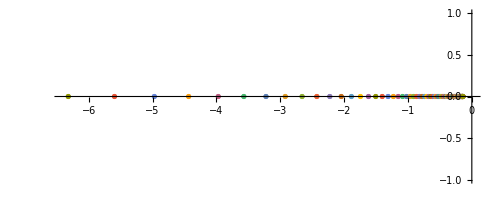

```mathematica
ComplexListPlot[data]
```

Generating function for a 3*L strip

```mathematica
Clear[z]
Clear[L]
```

```mathematica
L=500;
T=({{1+z, 0, 0, 0, 1, 1, 1, z^2+2z, z, 2 z^2}, {3z, 0, 0, 0, 2z, z, 0, 4 z^2, 2 z^2, 0}, {3 z^2, 0, 0, 0, z^2, 0, 0, 2 z^3, z^3, 2 z^4}, {z^3, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}});
```

```mathematica
Subscript[v, i] = {1+z,3z,3 z^2,z^3,0,0,0,0,0,0};
v = MatrixPower[T,L-1].Subscript[v, i];
g[z_]=v[[1]]//Expand;
f[z_]=z;
j = Roots[g[z]==0,z]//FullSimplify;
```

1+794 z+311860 z^2+80784738 z^3+15525826515 z^4+2361223401024 z^5+295990161339576 z^6+31454413390440264 z^7+2892519851312095809 z^8+233814864119337048377 z^9+16820338179167904476473 z^10+1087675667547203497575248 z^11+63744157743045121422762756 z^12+3409210405423598455044310401 z^13+167373391288655559472534308114 z^14+7581036993980767590390703634769 z^15+318187743056886802039180068253833 z^16+12422780938814592239886476223990216 z^17+452697228429316632397374900372469099 z^18+15444016589413906426470204698863576079 z^19+494592661588187164950531245585259210730 z^20+14904711926048691867656333952709306214907 z^21+423584350907992310165886055884518626329135 z^22+11375235135780236940589047601964252908500600 z^23+289182373923675633162003437928111401703784638 z^24+6970973521115597048907239740813111693213144845 z^25+159582310535672986645293905083798654974304951290 z^26+3474179790824454285525169888685202059267999490761 z^27+72020362463778845443629969154658139596854223102206 z^28+1423346620112773459600211590419466025428272778305776 z^29+26847087540962279509407031995639278348026717756363659 z^30+483792540867798056221221387066231242850529221128897505 z^31+8336999803238197465016393565082758075495875595709141569 z^32+137509852845733800691209718725133462752060339793080121023 z^33+2172651747149702191654904683979084060574079244744237219373 z^34+32908938067507902136649415263979263741214345402253505571672 z^35+478209811178501756594928040901830915445520384829769804000724 z^36+6671098530538068329453072938849714762622735634554974298641095 z^37+89397506759242282080517051533292754849639136663145728156381852 z^38+1151490781797204975893880793545684903954844918540209044364645267 z^39+14264104557234257722097576159345842069319548533784411654510493748 z^40+170021877038607286947768855452295385388628741384833580961857413514 z^41+1950989289541747880043327634887631416006883061433374255439099694917 z^42+21562320247692445358075006745806406283143496186532560992636988422387 z^43+229623007490734506046951535884762604246243960778894276135108873476877 z^44+2357176884467026000357471281391269792959107784683075657835522556047817 z^45+23334196368687373800457920655847843301358601890717394168669118535161603 z^46+222830466118345480689531443062459372731981093840370433772657736657492518 z^47+2053454854462868259533075607930459373243261667638982396294532771084825231 z^48+18266849605992460304509105031679021411772995061330062077954508974668425399 z^49+156906442998119161072922823001186787441905065112101281277871687218773631018 z^50+1301785404271113659561361833477523775665068923855684180129058402480971183875 z^51+10434579021782903835803792829919571394903281082591154392278378887199162048589 z^52+80826863910474738020739176393364076169779978907106944702834377591226024532048 z^53+605178395874011346664593242458036636289039449942187066519508974478202070425935 z^54+4380798031133658571802939894358578903882861718018008475715677773652858890893479 z^55+30665801524657328992532004332509984859981601759697892869243024254757839413739111 z^56+207620397839487949834614503356790766517719418870262969805232528245728681695026429 z^57+1359809629895112376427448448214883339981103536418483195290617735648981021735438619 z^58+8616900559241149215434754633215202799403942123870667835980521736890484061725391986 z^59+52839211259711755693027633053556082553904031473218515263046845439100872743398656664 z^60+313585795678155210711261010240572099440001044396972830306591101310962354483005044767 z^61+1801395681109896547844513009806628757480029829372798569694706515408831972546311872710 z^62+10017697572763942511474621623007676922020197306425495092928178848118592430175042434477 z^63+53936388152052651453732489820046282892972251144324013184579369307844310177607740397513 z^64+281187420760112429819999445590683545798736280879817140203814937493426170246013633395562 z^65+1419550841569942846621153184806172365653492618502499661443321924388517957620189129420825 z^66+6940394595690798782536892175217282032687779464450745110948078985814917483831080605225297 z^67+32864644026486079347472312496821478060966165623665965999042809831894402764783453996244440 z^68+150735344937518967501673620186334934460513958270241275675860134949293080633975414455447579 z^69+669682659208001362209971930788471848684408771136025097571344536819584528443885613996070733 z^70+2882131924899398135972003454506908883861785840234264632423638595232154299492992896038590762 z^71+12016260875851191753046656484785482185797757040922161988610018456730045782413206261227790064 z^72+48534689866672732516716542607452391531993131730012394631746146917468739031444528177608918405 z^73+189922449838631170179903308892416886891795648459016095201535182314409497104668051497491040496 z^74+720032804408202123267050121668302934835057472844761943518558579038376744489664366682592731357 z^75+2644771604939792786479715795194704754455708725621861104150684901694076925650963403737858216290 z^76+9412158123538235852438830252097130054179561362821856027438154011872632622224964282149306288952 z^77+32453234964773226270175234890020305103569655327133099672304512735469840260173285382817747275237 z^78+108416286443110289900134912449012247900656395594860955021738312451870268987293361986583092408093 z^79+350910477173211610859160582806023062047865776928468340899272844950097641994327127636180520558724 z^80+1100420106315431929395665903687305236375484008727455671580739697157452173040926214890608647545189 z^81+3343288251637540721866819635815423120036450040580716103309257903540905905528367526765253882200473 z^82+9840852400027343325408321749935207091336454838972043076393165392324557958522411581130976264994078 z^83+28062312374306498877443768041586608388777169469253094691793200440223791052158499008483984216286581 z^84+77523277994170637537242121510519784531624742576711618342063023855778939114296681018102237600194367 z^85+207463996781134468264910101486462179131708669272569614253005579096808206894574079068774988120166310 z^86+537820381434831741716255447392437037188270989519165078212844826460926992992723427249739656418416781 z^87+1350503332716410064071156719187251994806218967383002637148157552610986200112923011501035957373216912 z^88+3284702244182048016802019071223105098040868389635377338685495534752554448104231363755557037377532360 z^89+7737746086895863711728695565357811597043774755049396137284458848859647285445828670382043572197254545 z^90+17653279951861824505465156696218940787544355315858557534873949328554680677293027461733429185997418669 z^91+39003301670290118965047274204621441672227170598965226013596102829614394240628854682395535386947303757 z^92+83447472339655829745732987775564920063495351053745030050662670008235888831857825310555249390893409505 z^93+172874115727081815332478492328592543630543258035159966215708082081676548651914984382485652303960173993 z^94+346752169360119584266001644740090079600291944221038874746806629141575275414006468086683982215703693052 z^95+673358991707748708996955313484426904005329530649267417167186509386487189732140649721308249707691934884 z^96+1265833665681161545211032282605006479323208709125172079024972531937311758210692747793230811454355187723 z^97+2303412913044832294147275931815109428382382986526350566499599285141345314210609175043267834688629561344 z^98+4056890366797709620280413931922634493390345975848279062796841083661382975162496004067553762719498378849 z^99+6915135535736552085084803439300901229070762597551916997868623235381687902626183036951666694042339088394 z^100+11406495059078234790899040371890364348937481028454001999185218228329902165724051573309653667203233516124 z^101+18205579487520046081524452552630616436855034923742934167443349575290108780523134613475510696082619712142 z^102+28113362404823556029559959179232262180081380709180597857681109452226891566340213145987174934470737301233 z^103+41998216850164858367463081368894525496483469918149084599884911942753850597387525595265495014952064249125 z^104+60689148219975191616531149307549511148276626942782056936927911697085694983241176331156272179500898673384 z^105+84821176547456755327904758434840541029794563983716753713508491433041259002425077383236917551507761953730 z^106+114646317795005835427073978288684034850523578683365022782385335942668202889546699504227529538823288616495 z^107+149839593042027674136336055371798500680458940366257759516939701256830148501586340093530741791211150405747 z^108+189343489568475180801740165373226808162122364248746306701440912740756460480984731807013005608271891644792 z^109+231300576594615537167029373547166089341212994578732996777934587915849055418214449605150610159409997734831 z^110+273117409635031671672221238433363459967656627525217284603050054781673435467664175978048229355855115813264 z^111+311681273268717804295171708724715315245458892486274182583727471578040821752865032528085851311527884901396 z^112+343717413542818610357526006490862961982900202847370336603371131303184303174017582896847260599098231865201 z^113+366236147074281993354162960550387388582837857063040545107691360263578146414664524844014471052111914605537 z^114+376988011947055264162835602286837453296132135685521014429958109621514650866827677841836047032741472250259 z^115+374832115774070477542204453213223383360514028489325515832585226690903398445580502096022027665736943263445 z^116+359934631857211003067608015808479256711251903193601838631707452268582404962969709134600081246613389183523 z^117+333749864394150887699499778870155446066432965769314527798997883322324820520066418149981997800155490509923 z^118+298786207031044656427848221544623308978328495669026779768937210130877934376246105822297043616115517531189 z^119+258209145828552122815942172732232476680859036470355292687066111408512025721561151273124363629704744458702 z^120+215368509073580710430664950501756396800580698214475290545426631772883894299303800438304411763488679883997 z^121+173347802702098690792287719750242563198766608548681603927841117524273957672458241584486750717137573925878 z^122+134618334918331492014648127140190225731602562461469362722823411548698426491361630361110904437529730325132 z^123+100846784802327709874477363738035165008789645530148135417690374319072084630781097409076972317181559816472 z^124+72863846917226815667611364822165059594182515651589986945067052708705296502283846083092098634037838300772 z^125+50765946656550944259543445821632774834134554835155081065462731140892857765955632858442838643020837011524 z^126+34100381841506409572282012866158286212531198928356638143617955547502548890647776641488965296707268038681 z^127+22079342654467461586811323213858855893420071856231792626796545644339630999782765130632049883712691523514 z^128+13777317313914061565917832530320121628861217375009449282335927284901508811572220106257247797569310436794 z^129+8283309673576726101972829943434276836024076427678268090402849904928285960825800756476871345462493056356 z^130+4797450073408980342043046238727402908115700019798046559090884172796371236299625778518247699682218173761 z^131+2676014131617274084454397374209089098716213595874968815383360337659503830229513237471893837070165261100 z^132+1437272416841750466049094293130268599389811545071004435866370942113932419405952324436598845566627091600 z^133+743123742868296178177200339243342792308163014668105827857203331785345888084685288122073867464053528732 z^134+369785838187104957906062582115338541782137331630842877161190875660028197682952728767673116145548643118 z^135+177051353375518827449040812191738407739008459899000691727749062876234393365771317512461977860537078208 z^136+81545069983319930328591240724871004465114128499124227179973774647309788442684475559596832784896960683 z^137+36118696696064820393374756870124973651510336462771868569591397538599633543793133733128832044501269159 z^138+15381029302004457440569680345936684487051251534125721345633739071377261937069677149255956952895803584 z^139+6295602103320361919832429870541266405592735831442296462960271525066856693466381851476785703858529939 z^140+2476074066661769452536827594942976180440101325811175496284135019054943431585562025964479864970725023 z^141+935484593193898749958833893286575950026107095987141319076113221870568187716957715126449231980436886 z^142+339409904937032718695704213558341012085026920036035254231641572742596676356307625395320237584235971 z^143+118220108293899455635170634096235799880135571140008072871127819816404374979763426202362336010370543 z^144+39518183096756875291773077339718484738262733078258730806472161174515725922684689377350258384657048 z^145+12673503193887791577953090798497301901974857378177560937877901698344604143731931831112098714308202 z^146+3897993415762277462149859949226992682153036612151823960575411214167346578663825933535371328920004 z^147+1149412549291943262490449512300941731893019664697417128674135150882903939243864389498533529719122 z^148+324819214622636886737503466761764833190522813070125847185616034031496884345346009432706071010508 z^149+87937383881560331239016662334848006651930380655058979794640192586397413423091817345690839312049 z^150+22798213682935147469287978382383473308363679345480290913104787013604552875567919015865958649010 z^151+5657791319906239460951833659728977177025759147148749112977977407200862057731905188734011121214 z^152+1343472793015780430418962230107038401653836433383261077546561634752129682660663832929330048235 z^153+305110365938180803756381265554089659013166465136269158026146123684083987536412249531461725116 z^154+66242137970209221074633808734815008661144496668984276902501688331633224753043929398312108096 z^155+13742210042855894126593612646493294927829319311529100046865560812460568599902722393230379541 z^156+2722771411232191152241628045052607256940563306817555307120575740542467213045275098220163396 z^157+514964168929843233004485519793069418959266651905101863391886650820552275105748107432943463 z^158+92923105651838908603675801214248573438296036252612666226185309472796770864053643054132077 z^159+15988622110520858152310778148101407791265097145032348309182296393997411483431867953461946 z^160+2621730660340749626526601325254194625614155357739472583279839536116656411689382079279685 z^161+409442042130861814047545345502458249489604513386982109926086058714285141994533204510153 z^162+60862434985032730544385097974196408413049582231979637988395401148848863758066167724915 z^163+8605388573120061663996523577207552833408243734538705398767219338855548136263574567791 z^164+1156519718007961073566253635441177521425468845834189572848925615268770318635175253221 z^165+147631208753420744129123441394853144616746586118029428214851625582196424042995960171 z^166+17885852863706085856538415185710025213599595081087803938998194819487701393780230969 z^167+2054906920963385643289705905637416351056963911734591736428696811158769588038570879 z^168+223691447717181931449385035277586577541323506655126533097249340712959322496481509 z^169+23050582731350681168707661864221580482232753465578865302551554496255122574279750 z^170+2246284487155352074525859770835856400292560436464238980491030424521835288264997 z^171+206797171773062323327527797179827456926872356388455581142706791618820397466421 z^172+17965385844219818871576429014395301992445333751914929331299085766824307026828 z^173+1471026650668023974451097575537297755245818914706987917195359104121991855553 z^174+113380155274494035861695246582923555783943666084699423456579753463516422701 z^175+8214519953077473949456932544071671779123870096432181018351923083460827294 z^176+558601378775081130961459145180653362964087673274230236522489406370292791 z^177+35594732707220539632482759443888336011748430421572731510468461207053700 z^178+2121572741166951169922768910270353658289581716972336434458228649117401 z^179+118050822683800509996722183571464164780477403106560835445492251355257 z^180+6119051723475085846559037635886685162627211232019958519701605381432 z^181+294760642072970996068132986442705670962587754064267798375623562310 z^182+13160610634039303245042466193142252518942300353849453112416247661 z^183+543024104866468980316456500533532858957955812374836010984439594 z^184+20637321644448166236958240195996818482693588986866001791956670 z^185+719682613596007709437348347081429098393769098603114060209845 z^186+22930405963244126322492057442105076512104292764208727440764 z^187+664217194696187437537321122048967069776675338307562534644 z^188+17391081991977279122942168821190455222222673387204365101 z^189+408793924020524034516285103393315748805836658460201923 z^190+8556789358226877176278562716214062327708171429454808 z^191+157926125311517826746456701996938314162059859279682 z^192+2538711049205486348245381994390082148447467161097 z^193+34996543789555642998614567379646870454775933456 z^194+405332993170614280465164124699289660341063266 z^195+3835461238316687656182815375442892953723624 z^196+28470350663686595829839371474378246750440 z^197+155449528936410427942040535860048552011 z^198+555055373725129247016901877290317161 z^199+972248041367800504724352407998099 z^200

{0.03125,{{-11.85331359},{-11.2612691},{-10.7187631},{-10.17350191},{-9.64626001},{-9.141665853},{-8.653104798},{-8.186499739},{-7.740323578},{-7.315194046},{-6.911500051},{-6.528830718},{-6.167036597},{-5.825670991},{-5.504129163},{-5.201774118},{-4.917847702},{-4.651535783},{-4.402000249},{-4.16836795},{-3.949760018},{-3.745308008},{-3.554153081},{-3.375460098},{-3.208426943},{-3.052282327},{-2.906291829},{-2.769764014},{-2.642045104},{-2.522519645},{-2.410617676},{-2.305805781},{-2.20757987},{-2.115483268},{-2.029095012},{-1.947985604},{-1.87178908},{-1.800244496},{-1.732795081},{-1.668952685},{-1.610326343},{-1.552992095},{-1.464804374},{-1.135894899},{-1.045781194},{-0.9751437325},{-0.9139293064},{-0.8590496195},{-0.8090847283},{-0.7632211062},{-0.7209191088},{-0.6817821286},{-0.6454970504},{-0.6118041788},{-0.5804807625},{-0.5513313341},{-0.524181693},{-0.4988749458},{-0.4752687595},{-0.4532333624},{-0.4326500197},{-0.413409824},{-0.3954127014},{-0.3785665685},{-0.3627866015},{-0.3479945888},{-0.3341183488},{-0.3210912003},{-0.3088514742},{-0.2973420603},{-0.2865099807},{-0.2763059853},{-0.2666841615},{-0.2576015527},{-0.2490177756},{-0.2408946274},{-0.2331956569},{-0.2258859057},{-0.2189278976},{-0.2123305176},{-0.2062158036},{-0.1522923315},{-0.1421437415},{-0.1351092257},{-0.1294060762},{-0.1244987446},{-0.1201460309},{-0.1162160534},{-0.1126274972},{-0.1093258478},{-0.1062722078},{-0.1034374501},{-0.1007989125},{-0.09833841242},{-0.09604099264},{-0.09389409781},{-0.09188701336},{-0.09001047215},{-0.08825637129},{-0.0866175633},{-0.08508769901},{-0.083661107},{-0.0823326995},{-0.08109789787},{-0.07995257272},{-0.07889299513},{-0.07791579664},{-0.07701793594},{-0.07619667105},{-0.07544953589},{-0.0747743204},{-0.0741690537},{-0.07363198975},{-0.07316159522},{-0.07275653912},{-0.07241568415},{-0.07213807949},{-0.07192295491},{-0.07176971603},{-0.07167794083},{-17.53784707-3.45381531 ⅈ},{-17.53784707+3.45381531 ⅈ},{-17.3391482-3.34927328 ⅈ},{-17.3391482+3.34927328 ⅈ},{-17.01926488-3.1745389 ⅈ},{-17.01926488+3.1745389 ⅈ},{-16.59263528-2.92970352 ⅈ},{-16.59263528+2.92970352 ⅈ},{-16.07598706-2.61655426 ⅈ},{-16.07598706+2.61655426 ⅈ},{-15.48381395-2.23953771 ⅈ},{-15.48381395+2.23953771 ⅈ},{-14.82905311-1.80284741 ⅈ},{-14.82905311+1.80284741 ⅈ},{-14.12381536-1.32234141 ⅈ},{-14.12381536+1.32234141 ⅈ},{-13.35333397-0.81453159 ⅈ},{-13.35333397+0.81453159 ⅈ},{-12.52633841-0.23066099 ⅈ},{-12.52633841+0.23066099 ⅈ},{-1.483117117-0.026227167 ⅈ},{-1.483117117+0.026227167 ⅈ},{-1.422350664-0.085449508 ⅈ},{-1.422350664+0.085449508 ⅈ},{-1.377296064-0.120735445 ⅈ},{-1.377296064+0.120735445 ⅈ},{-1.339228562-0.15461094 ⅈ},{-1.339228562+0.15461094 ⅈ},{-1.319479132-0.08490298 ⅈ},{-1.319479132+0.08490298 ⅈ},{-1.306413934-0.179203463 ⅈ},{-1.306413934+0.179203463 ⅈ},{-1.285408742-0.123750398 ⅈ},{-1.285408742+0.123750398 ⅈ},{-1.280562682-0.191822488 ⅈ},{-1.280562682+0.191822488 ⅈ},{-1.263412898-0.192733721 ⅈ},{-1.263412898+0.192733721 ⅈ},{-1.259134272-0.175613372 ⅈ},{-1.259134272+0.175613372 ⅈ},{-0.2031843616-0.0040458612 ⅈ},{-0.2031843616+0.0040458612 ⅈ},{-0.1989252718-0.0098863141 ⅈ},{-0.1989252718+0.0098863141 ⅈ},{-0.194328464-0.0147992014 ⅈ},{-0.194328464+0.0147992014 ⅈ},{-0.189778627-0.0189821225 ⅈ},{-0.189778627+0.0189821225 ⅈ},{-0.1853850559-0.0225627941 ⅈ},{-0.1853850559+0.0225627941 ⅈ},{-0.1812099113-0.0256349993 ⅈ},{-0.1812099113+0.0256349993 ⅈ},{-0.1773024779-0.0282594716 ⅈ},{-0.1773024779+0.0282594716 ⅈ},{-0.173686441-0.0304682209 ⅈ},{-0.173686441+0.0304682209 ⅈ},{-0.1703592762-0.0323006453 ⅈ},{-0.1703592762+0.0323006453 ⅈ},{-0.1698369876-0.0163465533 ⅈ},{-0.1698369876+0.0163465533 ⅈ},{-0.1673391948-0.0338137804 ⅈ},{-0.1673391948+0.0338137804 ⅈ},{-0.1646675386-0.03502449 ⅈ},{-0.1646675386+0.03502449 ⅈ},{-0.1641604532-0.0280681799 ⅈ},{-0.1641604532+0.0280681799 ⅈ},{-0.1623555193-0.0359480824 ⅈ},{-0.1623555193+0.0359480824 ⅈ},{-0.1608017088-0.0328906557 ⅈ},{-0.1608017088+0.0328906557 ⅈ},{-0.1604579279-0.036593196 ⅈ},{-0.1604579279+0.036593196 ⅈ},{-0.1590213098-0.0369558506 ⅈ},{-0.1590213098+0.0369558506 ⅈ},{-0.1589276063-0.0353673921 ⅈ},{-0.1589276063+0.0353673921 ⅈ},{-0.1581491314-0.0370146454 ⅈ},{-0.1581491314+0.0370146454 ⅈ},{-0.158107851-0.0366127702 ⅈ},{-0.158107851+0.0366127702 ⅈ}}}

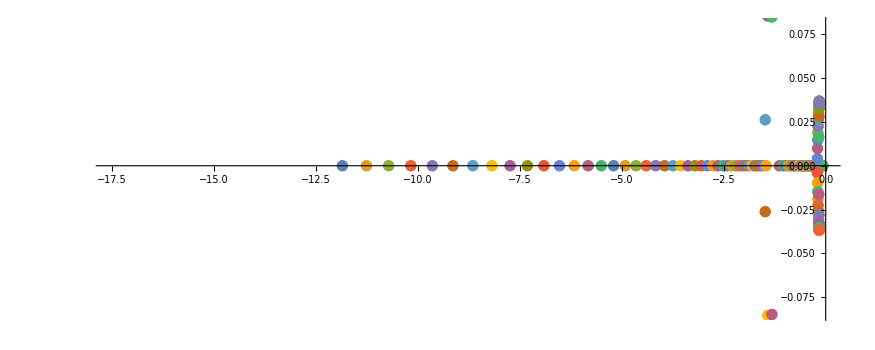

```mathematica
Timing[data = Table[f[z]/.Solve[N[j[[i]],10]],{i,1,L}]]
ComplexListPlot[data, AspectRatio->Full]
```

```mathematica
func1[x_]:= x[[1]];
data2 =func1/@data;
num_real = Length[Cases[data2,_Real]];
num_complex = Length[Cases[data2,_Complex]];
g2[data_]:= Length[Cases[func1/@data,_Real]]/Length[Cases[func1/@data,_Complex]]
N[g2[data]]
```

2.75

```mathematica
myfunc1[data_]:=
Module[{y},
y=data;
func1[x_]:= x[[1]];
data2 =func1/@y;
N[Length[Cases[data2,_Real]]/Length[Cases[data2,_Complex]]]
]
```

```mathematica
myfunc1[data]
```

1.25

```mathematica
myfunc2[L_]:=
Module[{p},
T=({{1+z, 0, 0, 0, 1, 1, 1, z^2+2z, z, 2 z^2}, {3z, 0, 0, 0, 2z, z, 0, 4 z^2, 2 z^2, 0}, {3 z^2, 0, 0, 0, z^2, 0, 0, 2 z^3, z^3, 2 z^4}, {z^3, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}});
Subscript[v, i] = {1+z,3z,3 z^2,z^3,0,0,0,0,0,0};
p= MatrixPower[T,L-1].Subscript[v, i];
g[z_]:=p[[1]];
f[z_]:=z;
j = Roots[g[z]==0,z];
data = Table[f[z]/.Solve[N[j[[i]],10]],{i,1,L}];
myfunc1[data]]
```

```mathematica
myFunction[x_]:=
Module[{y},y=x;
y=y+3;
(y+3)^3]
```

```mathematica
myFunction[5]
```

1331

```mathematica
myfunc2[10]
```

4.

```mathematica
llist = Range[10,150,5]
```

{10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150}

```mathematica
fraclist=myfunc2/@llist
```

{4.,2.75,2.33333,3.16667,1.5,1.5,1.85714,1.8125,2.125,1.75,2.,1.95455,1.69231,1.67857,1.66667,1.65625,1.8125,1.63889,1.77778,1.625,1.61905,1.5,1.5,1.5,1.6,1.5,1.5,1.5,1.5}

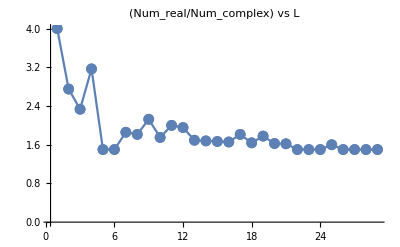

```mathematica
ListLinePlot[fraclist,PlotRange->All,Mesh->Full,PlotLabel->"(Num_real/Num_complex) vs L"]
```

```mathematica
Abs[Cases[data2,_Real][[1]]]
Abs[Cases[data2,_Complex][[1]]]
```

12.08675331

17.8194278

```mathematica
func3[y_,z_]:= If[Abs[Re[z]]>Abs[Re[y]],z,y]
```

```mathematica
func3[2,1]
```

2

```mathematica
myfunc3[data_]:=
Module[{y},
y=data;
func1[x_]:= x[[1]];
data2 =func1/@y;
Abs[func3[Cases[data2,_Real][[1]],Cases[data2,_Complex][[1]]]]
]
```

```mathematica
myfunc3[data]
```

17.8194278

```mathematica
myfunc4[L_]:=
Module[{p},
T=({{1+z, 0, 0, 0, 1, 1, 1, z^2+2z, z, 2 z^2}, {3z, 0, 0, 0, 2z, z, 0, 4 z^2, 2 z^2, 0}, {3 z^2, 0, 0, 0, z^2, 0, 0, 2 z^3, z^3, 2 z^4}, {z^3, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}});
Subscript[v, i] = {1+z,3z,3 z^2,z^3,0,0,0,0,0,0};
p= MatrixPower[T,L-1].Subscript[v, i];
g[z_]:=p[[1]];
f[z_]:=z;
j = Roots[g[z]==0,z];
data = Table[f[z]/.Solve[N[j[[i]],10]],{i,1,L}];
myfunc3[data]]
```

```mathematica
myfunc4[15]
```

11.14610877

```mathematica
Abs[-17.4864629158096687045-3.4286472180760749582 ⅈ]
```

17.819427798108658368

```mathematica
llist2 = Range[10,150,5]
```

{10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150}

```mathematica
modlist = myfunc4/@llist
```

{10.10256814,11.14610877,13.41380292,14.60832335,15.47005875,16.06715619,16.42273348,16.70437978,16.92355744,17.08123199,17.21154149,17.31312189,17.39276969,17.46147037,17.51723048,17.56350707,17.60362713,17.63711689,17.66613493,17.69158873,17.71339481,17.73269272,17.74975272,17.76473277,17.77819593,17.79020047,17.8009301,17.81066233,17.8194278}

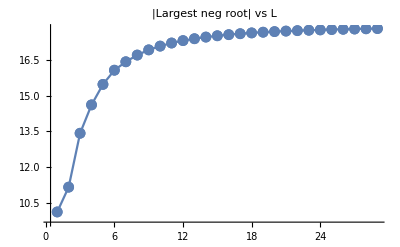

```mathematica
ListLinePlot[modlist,PlotRange->All,Mesh->Full,PlotLabel->"|Largest neg root| vs L"]
```

```mathematica
func4[y_,z_]:= If[Abs[Re[z]]<Abs[Re[y]],z,y]
```

```mathematica
Last[Cases[data2,_Real]]
Last[Cases[data2,_Complex]]
```

-0.07673442167

-0.1768213664+0.0325294256 ⅈ

```mathematica
func4[Last[Cases[data2,_Real]],Last[Cases[data2,_Complex]]]
```

-0.07673442167

```mathematica
myfunc5[data_]:=
Module[{y},
y=data;
func1[x_]:= x[[1]];
data2 =func1/@y;
Abs[func4[Last[Cases[data2,_Real]],Last[Cases[data2,_Complex]]]]
]


myfunc6[L_]:=
Module[{p},
T=({{1+z, 0, 0, 0, 1, 1, 1, z^2+2z, z, 2 z^2}, {3z, 0, 0, 0, 2z, z, 0, 4 z^2, 2 z^2, 0}, {3 z^2, 0, 0, 0, z^2, 0, 0, 2 z^3, z^3, 2 z^4}, {z^3, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}});
Subscript[v, i] = {1+z,3z,3 z^2,z^3,0,0,0,0,0,0};
p= MatrixPower[T,L-1].Subscript[v, i];
g[z_]:=p[[1]];
f[z_]:=z;
j = Roots[g[z]==0,z];
data = Table[f[z]/.Solve[N[j[[i]],10]],{i,1,L}];
myfunc5[data]]

modlist2 = myfunc6/@llist
```

{0.08293876799,0.07673442167,0.07454346127,0.07351785348,0.07295535461,0.07261353133,0.07239026662,0.07223639968,0.07212586254,0.07204377871,0.07198115255,0.07193228357,0.0718934167,0.07186199637,0.0718362343,0.07181484867,0.07179690122,0.07178169237,0.07176869186,0.07175749186,0.07174777454,0.07173928923,0.07173183611,0.07172525426,0.07171941298,0.07171420517,0.07170954244,0.07170535126,0.07170157013}

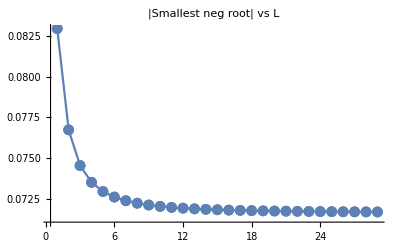

```mathematica
ListLinePlot[modlist2,PlotRange->All,Mesh->Full,PlotLabel->"|Smallest neg root| vs L"]
```

Some code to transform into the new basis

```mathematica
A = ({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/3, 0, 0, 2z/3, z/3, 2z^2/3}, {0, 0, 0, 0, 0, 1/3, 0, z^2/3, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 1/3, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1/3, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1/3, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, z/3, 0, 0, z^2/3, 0, 0}, {0, 0, 0, 0, 0, z^2/3, 0, 0, 0, 0}, {0, 0, 0, 0, z/3, 0, 0, 0, 0, 0}});
U = Inverse[A]*T
```

{{False (1+z),0,0,0,False,False,False,False (2 z+z^2),False z,2 False z^2},{3 False z,0,0,0,2 False z,False z,0,4 False z^2,2 False z^2,0},{3 False z^2,0,0,0,False z^2,0,0,2 False z^3,False z^3,2 False z^4},{False z^3,0,0,0,0,0,0,0,0,0},{0,False,0,0,0,0,0,0,0,0},{0,0,False,0,0,0,0,0,0,0},{0,0,0,False,0,0,0,0,0,0},{0,0,0,0,False,0,0,0,0,0},{0,0,0,0,0,False,0,0,0,0},{0,0,0,0,0,0,0,False,0,0}}

```mathematica
h = Roots[CharacteristicPolynomial[T,x]==0,x]
```

x==Root[4 z^9+2 z^8 #1+(-8 z^6+6 z^7) #1^2+(-10 z^5-4 z^6) #1^3+(2 z^4+z^5+z^6) #1^4+(-5 z^3+z^4) #1^5+(-2 z^2-2 z^3+z^4) #1^6+(-z-5 z^2-2 z^3) #1^7-2 z #1^8+(-1-z) #1^9+#1^10&,1]||x==Root[4 z^9+2 z^8 #1+(-8 z^6+6 z^7) #1^2+(-10 z^5-4 z^6) #1^3+(2 z^4+z^5+z^6) #1^4+(-5 z^3+z^4) #1^5+(-2 z^2-2 z^3+z^4) #1^6+(-z-5 z^2-2 z^3) #1^7-2 z #1^8+(-1-z) #1^9+#1^10&,2]||x==Root[4 z^9+2 z^8 #1+(-8 z^6+6 z^7) #1^2+(-10 z^5-4 z^6) #1^3+(2 z^4+z^5+z^6) #1^4+(-5 z^3+z^4) #1^5+(-2 z^2-2 z^3+z^4) #1^6+(-z-5 z^2-2 z^3) #1^7-2 z #1^8+(-1-z) #1^9+#1^10&,3]||x==Root[4 z^9+2 z^8 #1+(-8 z^6+6 z^7) #1^2+(-10 z^5-4 z^6) #1^3+(2 z^4+z^5+z^6) #1^4+(-5 z^3+z^4) #1^5+(-2 z^2-2 z^3+z^4) #1^6+(-z-5 z^2-2 z^3) #1^7-2 z #1^8+(-1-z) #1^9+#1^10&,4]||x==Root[4 z^9+2 z^8 #1+(-8 z^6+6 z^7) #1^2+(-10 z^5-4 z^6) #1^3+(2 z^4+z^5+z^6) #1^4+(-5 z^3+z^4) #1^5+(-2 z^2-2 z^3+z^4) #1^6+(-z-5 z^2-2 z^3) #1^7-2 z #1^8+(-1-z) #1^9+#1^10&,5]||x==Root[4 z^9+2 z^8 #1+(-8 z^6+6 z^7) #1^2+(-10 z^5-4 z^6) #1^3+(2 z^4+z^5+z^6) #1^4+(-5 z^3+z^4) #1^5+(-2 z^2-2 z^3+z^4) #1^6+(-z-5 z^2-2 z^3) #1^7-2 z #1^8+(-1-z) #1^9+#1^10&,6]||x==Root[4 z^9+2 z^8 #1+(-8 z^6+6 z^7) #1^2+(-10 z^5-4 z^6) #1^3+(2 z^4+z^5+z^6) #1^4+(-5 z^3+z^4) #1^5+(-2 z^2-2 z^3+z^4) #1^6+(-z-5 z^2-2 z^3) #1^7-2 z #1^8+(-1-z) #1^9+#1^10&,7]||x==Root[4 z^9+2 z^8 #1+(-8 z^6+6 z^7) #1^2+(-10 z^5-4 z^6) #1^3+(2 z^4+z^5+z^6) #1^4+(-5 z^3+z^4) #1^5+(-2 z^2-2 z^3+z^4) #1^6+(-z-5 z^2-2 z^3) #1^7-2 z #1^8+(-1-z) #1^9+#1^10&,8]||x==Root[4 z^9+2 z^8 #1+(-8 z^6+6 z^7) #1^2+(-10 z^5-4 z^6) #1^3+(2 z^4+z^5+z^6) #1^4+(-5 z^3+z^4) #1^5+(-2 z^2-2 z^3+z^4) #1^6+(-z-5 z^2-2 z^3) #1^7-2 z #1^8+(-1-z) #1^9+#1^10&,9]||x==Root[4 z^9+2 z^8 #1+(-8 z^6+6 z^7) #1^2+(-10 z^5-4 z^6) #1^3+(2 z^4+z^5+z^6) #1^4+(-5 z^3+z^4) #1^5+(-2 z^2-2 z^3+z^4) #1^6+(-z-5 z^2-2 z^3) #1^7-2 z #1^8+(-1-z) #1^9+#1^10&,10]

```mathematica
Solve[h[[1]]]
```

{{x→Root[4 z^9+2 z^8 #1+(-8 z^6+6 z^7) #1^2+(-10 z^5-4 z^6) #1^3+(2 z^4+z^5+z^6) #1^4+(-5 z^3+z^4) #1^5+(-2 z^2-2 z^3+z^4) #1^6+(-z-5 z^2-2 z^3) #1^7-2 z #1^8+(-1-z) #1^9+#1^10&,1]}}